## Calculating the quadrupole deformed potential (mean-field).

From
-Graphics-

```mathematica
ClearAll["Global`*"]
```

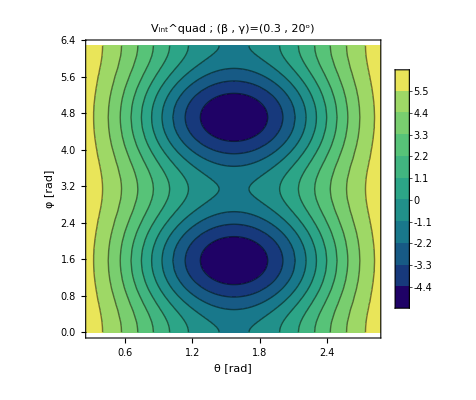

```mathematica
A=163;
β=0.3;
γ=20;
qPotential[beta_,gamma_,theta_,phi_]:=
206/A^(1/3)beta(Cos[gamma*π/180]*SphericalHarmonicY[2,0,theta,phi]+Sin[gamma*π/180]/(√2)(SphericalHarmonicY[2,2,theta,phi]+SphericalHarmonicY[2,-2,theta,phi]));
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
cplot[beta_,gamma_]:=ContourPlot[qPotential[beta,gamma,x,y],{x,0,π},{y,0,2π},Contours->10,AspectRatio->1,ClippingStyle->None,PlotLegends->Automatic,ContourStyle->Black,Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ [rad]","φ [rad]"},LabelStyle->{17,Bold,Black,FontFamily->"Times"},PlotRange->{{0.3,0.9π},Automatic},ColorFunction->"BlueGreenYellow",PlotLabel->StringTemplate["V_int^quad ; (β , γ)=(`` , (``)^o)"][beta,gamma]];
dplot[beta_,gamma_]:=DensityPlot[qPotential[beta,gamma,x,y],{x,0,π},{y,0,2π},AspectRatio->1,ClippingStyle->None,PlotLegends->Automatic,Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ [rad]","φ [rad]"},LabelStyle->{17,Bold,Black,FontFamily->"Times"},PlotRange->{{0.3,0.9π},Automatic}];
cplot[0.3,20]
```